```mathematica
(* ============================================================
   Basin of Attraction - Newton's Method in 1D
   Run each block one at a time (Shift+Enter).
   ============================================================ *)
```

```mathematica
(* ── STEP 1: Define the function and settings ─────────────────

   Change f, df, a, b to try different examples.
   f[x] = x^4 - 5x^2 + 4  has four roots: -2, -1, +1, +2      *)

f[x_]  := x^4 - 5 x^2 + 4
df[x_] := 4 x^3 - 10 x

(*f[x_]:=x^3-x
df[x_]:=3x^2-1*)

a    = -3.0;   (* left end of interval  *)
b    =  3.0;   (* right end of interval *)
n    = 2000;   (* number of starting points *)
tol  = 10^-8;  (* stop when step size < tol *)
nmax = 80;     (* max iterations allowed *)
```

```mathematica
(* ── STEP 2: Newton's method for one starting point ──────────

   Returns {limit point, number of steps, did it converge?}     *)

newtonStep[x0_] := Module[
  {x = N[x0], k = 0, step, dfval},

  While[k < nmax,
    dfval = df[x];

    (* avoid division by zero near a local extremum *)
    If[Abs[dfval] < 10^-12, dfval = 10^-12];

    step = f[x] / dfval;
    x    = x - step;
    k    = k + 1;

    If[Abs[step] < tol, Break[]]
  ];

  (* converged if we stopped early AND f is small there *)
  {x, k, k < nmax && Abs[f[x]] < 10^-5}
]
```

```mathematica
(* ── STEP 3: Run Newton from each starting point ─────────────*)

x0List = Table[a + (b - a) * i / (n - 1), {i, 0, n - 1}];

results    = Table[newtonStep[x0List[[i]]], {i, n}];
limitPts   = results[[All, 1]];
iterCounts = results[[All, 2]];
convQ      = results[[All, 3]];
```

```mathematica
(* ── STEP 4: Find the distinct roots ─────────────────────────

   Cluster the limit points: two counts as the same root
   if they are within rootTol of each other.                    *)

rootTol = 10^-4;

roots = {};
For[i = 1, i <= n, i++,
  If[convQ[[i]],
    pt = limitPts[[i]];
    (* add pt to roots only if it is not already there *)
    If[!MemberQ[roots, _?(Abs[# - pt] < rootTol &)],
      AppendTo[roots, pt]
    ]
  ]
];
roots  = Sort[roots];
nRoots = Length[roots];

Print["Found ", nRoots, " roots: ", roots]
```

Found 4 roots: {-2.,-1.,1.,2.}

```mathematica
(* ── STEP 5: Assign each starting point a root label ─────────

   rootLabel[[i]] = 1, 2, 3, ... for the root it converged to,
                  = 0 if it did not converge.                   *)

rootLabel = Table[
  If[convQ[[i]],
    (* find which root is closest to the limit point *)
    First @ Ordering[Abs[limitPts[[i]] - roots], 1],
    0   (* no convergence *)
  ],
  {i, n}
];
```

```mathematica
(* ── STEP 6: Assign a color to each starting point ───────────*)

palette = {Blue, Red, Darker[Green], Orange, Purple, Cyan};

pointColor[i_] :=
  If[rootLabel[[i]] == 0,
    Black,
    palette[[ rootLabel[[i]] ]]
  ]

colors = Table[pointColor[i], {i, n}];
```

```mathematica
(* ── STEP 7: Panel 1 - Basin of attraction ───────────────────

   Draw a thin vertical rectangle for each starting point,
   colored by which root Newton's method reaches.               *)

basinBars = Table[
  {colors[[i]],
   Rectangle[{x0List[[i]], 0}, {x0List[[i + 1]], 1}]},
  {i, 1, n - 1}
];

basinPlot = Graphics[
  basinBars,
  Frame       -> True,
  FrameLabel  -> {"x0 (starting point)", ""},
  PlotLabel   -> Style["Basin of Attraction", Bold, 13],
  AspectRatio -> 0.2,
  ImageSize   -> 700
];
```

```mathematica
(* ── STEP 8: Panel 2 - Iteration count ──────────────────────

   Color each bar by how many steps it took.
   White = converged fast.  Dark = converged slow.  Black = no convergence. *)

maxIter = Max[iterCounts];

iterShade[i_] :=
  If[convQ[[i]],
    GrayLevel[1 - (iterCounts[[i]] - 1) / maxIter],
    Black
  ]

iterShades = Table[iterShade[i], {i, n}];

iterBars = Table[
  {iterShades[[i]],
   Rectangle[{x0List[[i]], 0}, {x0List[[i + 1]], 1}]},
  {i, 1, n - 1}
];

iterPlot = Graphics[
  iterBars,
  Frame       -> True,
  FrameLabel  -> {"x0 (starting point)", ""},
  PlotLabel   -> Style["Iteration Count  (white=fast, gray=slow, black=no convergence)", Bold, 13],
  AspectRatio -> 0.2,
  ImageSize   -> 700
];
```

```mathematica
(* ── STEP 9: Panel 3 - Plot f[x] ────────────────────────────*)

funcPlot = Plot[
  f[x], {x, a, b},
  Frame       -> True,
  FrameLabel  -> {"x", "f(x)"},
  PlotStyle   -> {Blue, Thickness[0.003]},
  GridLines   -> Automatic,
  PlotLabel   -> Style["f(x)", Bold, 13],
  ImageSize   -> 700,
  (* mark the roots with colored dots *)
  Epilog -> Table[
    {PointSize[0.02], palette[[k]], Point[{roots[[k]], 0}]},
    {k, nRoots}
  ]
];
```

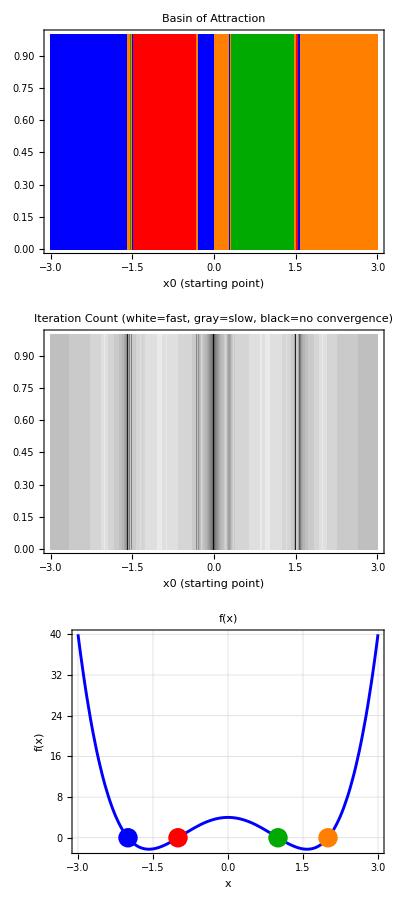

```mathematica
(* ── STEP 10: Show all three panels together ─────────────────*)

Column[{basinPlot, iterPlot, funcPlot}, Spacer[8]]
```